```mathematica
g = 9.8;
l = 1;
m = 1;
k = 1;
```

```mathematica
solutions = NDSolveValue[
{
r''[t]==r[t] θ'[t]^2+g Cos[θ[t]]-k/m (r[t]-l),
r[t]*θ''[t]+ 2r'[t]*θ'[t]+g Sin[θ[t]]==0,
r[0] == 1,r'[0]==6,
θ[0] == π/3, θ'[0]==10
},
{r[t],θ[t]},
{t,0,100}
];
```

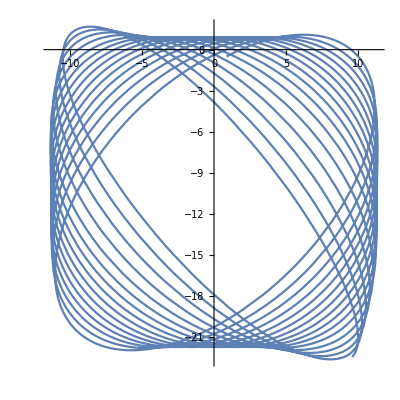

```mathematica
ParametricPlot[rV[t],{t,0,100},AspectRatio->1]
```

```mathematica
solutions
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

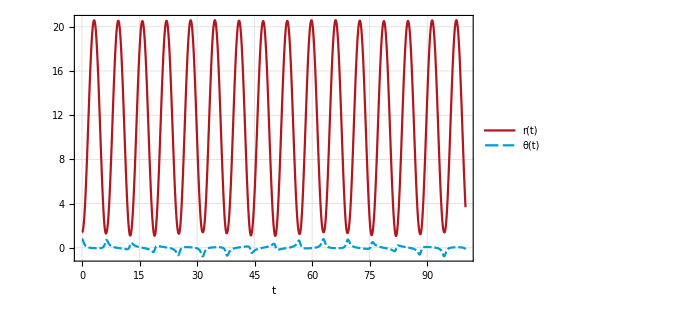

```mathematica
Plot[solutions,{t,0,100},
PlotRange->All,
PlotLegends->{"r(t)","θ(t)"},
PlotTheme->"Monochrome",
FrameLabel->{Style["t",15], Style["",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0, 0.61, 0.8300000000000001]}
]
```

```mathematica
rV[r_,θ_]:={r Sin[θ],-r Cos[θ]};
rV[tp_]:=Apply[rV,solutions/.t->tp];
```

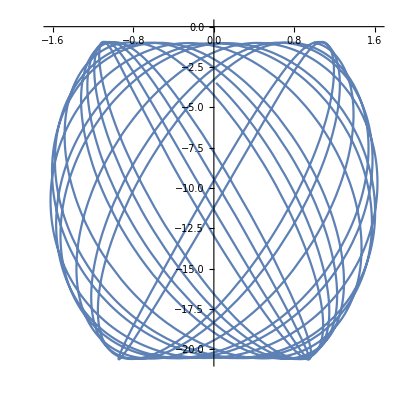

```mathematica
ParametricPlot[rV[t],{t,0,100},AspectRatio->1]
```